```mathematica
α=10^-5;(* - dissipation, α=ν/ω, ω->ω(1+ⅈα)*)
U=0.9;(* - anizatropy: p^2=4πe^2*n/m, b=eB/(mc), v=p^2/ω^2, u=b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα)*)
χ=10;(* - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L=1*) 
(*θ=0; - ngel between wave vector and XOZ*)
(*β=0; - angle between wave vector and magnetic field direction*)
(*P - wave polarisation; 2d-vector*)

(*=====================================================================================================================*)

(*Plasma configuration*)
X=3;(*plasma boundary*)
η=0.05;(*smoothing width, in parts of plasma whight*)
smoothingFunc=Function[x,(1-(x/X)^(2/η))^-1]; v=Function[x,((X^2-x^2)/(X^2-1))*smoothingFunc[x]*(1-ⅈ*α)];u=U(1-ⅈ*α);
ϵ=Function[x,1-v[x]/(1-u)];Subscript[ϵ, l]=Function[x,1-v[x]];g=Function[x,(√u)/(1-u)v[x]];
```

```mathematica
Subscript[n, y]=Cos[θ]Cos[β];Subscript[n, z]=Sin[θ];
M=({{0, -ⅈ Subscript[n, y] g[x]/ϵ[x], (Subscript[n, y] Subscript[n, z])/ϵ[x], 1-Subscript[n, y]^2/ϵ[x]}, {0, -ⅈ Subscript[n, z] g[x]/ϵ[x], -1+Subscript[n, z]^2/ϵ[x], -(Subscript[n, y] Subscript[n, z])/ϵ[x]}, {-Subscript[n, y] Subscript[n, z], Subscript[n, y]^2+g[x]^2/ϵ[x]-ϵ[x], ⅈ Subscript[n, z] g[x]/ϵ[x], -ⅈ Subscript[n, y] g[x]/ϵ[x]}, {Subscript[ϵ, l][x]-Subscript[n, z]^2, Subscript[n, y] Subscript[n, z], 0, 0}})//FullSimplify;
```

```mathematica
({{Sin[β], -Sin[θ]Cos[β], 0, 0}, {0, Cos[θ], 0, 0}, {0, 0, Sin[β], -Sin[θ]Cos[β]}, {0, 0, 0, Cos[θ]}}).({{1, 0, 0, -1}, {0, 1, 1, 0}, {0, -1, 1, 0}, {1, 0, 0, 1}})//Transpose;
Υ=Table[(%⟦i⟧)/Norm[%⟦i⟧],{i,1,4}]ᵀ//FullSimplify;
```

```mathematica
Δ=Inverse[Υ].M.Υ;
```

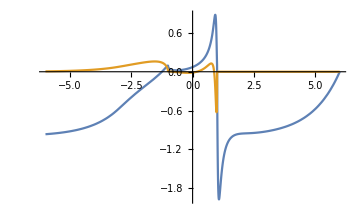
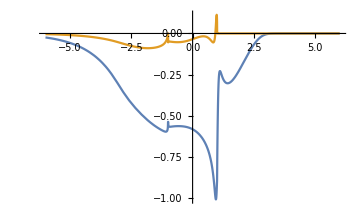
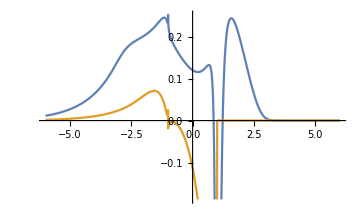
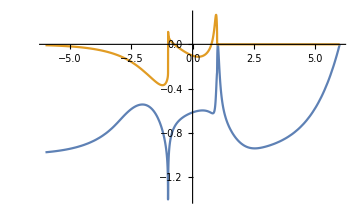

```mathematica
R=({{tt[x], st[x]}, {ts[x], ss[x]}});
A=R.Δ⟦{1,2},{3,4}⟧.R+R.Δ⟦{1,2},{1,2}⟧-Δ⟦{3,4},{1,2}⟧.R-Δ⟦{3,4},{3,4}⟧;
eq={D[R,x]==A};
ic={tt[2X]==0,st[2X]==0,ts[2X]==0,ss[2X]==0};
sol=NDSolveValue[{eq,ic}/.{θ->0.1,β->π/3},{tt,st,ts,ss},{x,-2X,2X}];
Table[Plot[{Re[sol⟦i⟧[x]],Im[sol⟦i⟧[x]]},{x,-2X,2X},ImageSize->Medium],{i,1,4}]
```